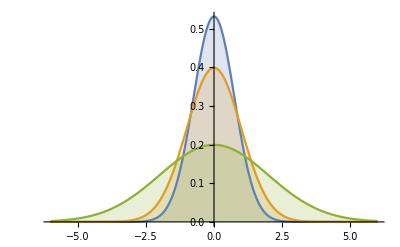

```mathematica
Plot[Evaluate@Table[PDF[NormalDistribution[0,σ],x],{σ,{.75,1,2}}],{x,-6,6},Filling->Axis]
```

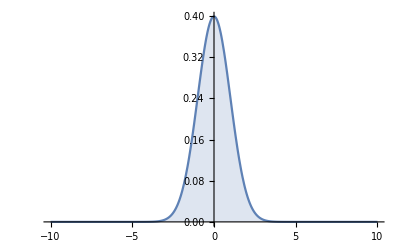

```mathematica
σ=1.0;
Plot[PDF[NormalDistribution[0,σ],x],{x,-10,10},Filling->Axis,PlotRange->Full]
```

```mathematica
Manipulate[Plot[PDF[NormalDistribution[0,σ],x],{x,-10,10},Filling->Axis,PlotRange->{0,0.1}],{σ,0.1,10}]
```

```mathematica
Manipulate[Plot[PDF[VonMisesDistribution[0,σ],x],{x,-π,π},Filling->Axis,PlotRange->{0,2.0}],{σ,0.1,100}]
```

```mathematica
σ = 0.1
sampleSize=10000;
(*randomTable=RandomVariate[NormalDistribution[0,σ],sampleSize];
anglesTable=Map[Function[x,π/2*(1-x)],randomTable];*)
anglesTable=RandomVariate[VonMisesDistribution[0,σ],sampleSize];
normalsTable=Table[{Sin[anglesTable[[i]]],Cos[anglesTable[[i]]]},{i,1,Length[anglesTable]}];
Table[Norm[normalsTable[[i]]],{i,1,Length[normalsTable]}];
averageLength=Sum[normalsTable[[i]][[2]],{i,1,Length[normalsTable]}]/Length[normalsTable]
```

0.1

0.0481934

```mathematica
functionSampleSize = 1000;
f[κ_]:=Sum[Cos[RandomVariate[VonMisesDistribution[0,κ]]],{i,1,functionSampleSize}]/functionSampleSize
```

```mathematica
f[1.0]
```

0.457009

```mathematica
bisou=Table[f[κ],{κ,0.1,100,1}]
```

{0.0664819,0.506442,0.703551,0.805322,0.87788,0.899271,0.909607,0.924141,0.936216,0.942336,0.955233,0.950036,0.954186,0.960438,0.965371,0.96551,0.969364,0.969398,0.972697,0.974429,0.973515,0.975054,0.9767,0.978922,0.980029,0.981044,0.980993,0.982197,0.983155,0.983664,0.984343,0.984228,0.984955,0.985213,0.986267,0.985881,0.986336,0.98576,0.987483,0.986189,0.987245,0.987861,0.988491,0.988437,0.987958,0.989181,0.98791,0.98942,0.989302,0.989582,0.989333,0.989904,0.990985,0.990867,0.990462,0.991244,0.990927,0.990858,0.991639,0.991953,0.991667,0.991469,0.991714,0.991679,0.992239,0.992431,0.992296,0.991982,0.991992,0.992478,0.993452,0.992771,0.992957,0.993111,0.992633,0.99343,0.993469,0.993996,0.993666,0.993256,0.993357,0.994167,0.993616,0.99417,0.99423,0.993597,0.993685,0.99431,0.994107,0.994228,0.994533,0.994547,0.994664,0.994675,0.994685,0.994984,0.994898,0.994632,0.994666,0.995053}

```mathematica
bisou2=Table[f[κ],{κ,0.1,20,1}]
```

{0.0424419,0.507776,0.707798,0.823886,0.870835,0.894034,0.919653,0.927072,0.936193,0.944579,0.949749,0.953902,0.957043,0.961916,0.964586,0.966668,0.969713,0.97211,0.971787,0.974448}

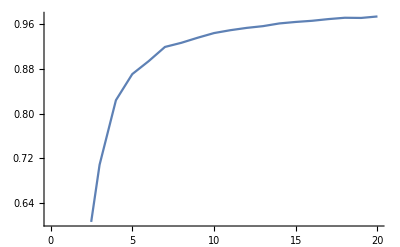

```mathematica
DiscretePlot[bisou2[[i]],{i,1,Length[bisou2]},PlotRange->{-0.1,1},Filling->Axis,ExtentSize->Full];
ListLinePlot[bisou2]
```

```mathematica
(*
 https://www.wolfram.com/mathematica/new-in-8/nonparametric-derived-and-formula-distributions/create-your-own-distribution.html
 *)
```

```mathematica
WrappedNormalPDF[θ_,σ_]:=Sum[Exp[(-(θ+2π k)^2)/(2 σ^2)],{k,-∞,+∞}]/(σ √(2π))
WNDist[σ_]:=ProbabilityDistribution[WrappedNormalPDF[x,σ],{x,-π,+π}]
(*WNDist[σ_]:=ProbabilityDistribution[N[Sum[Exp[(-(θ+2π k)^2)/(2 σ^2)],{k,-∞,+∞}]/(σ √(2π))],{θ,-π,+π}]*
```

```mathematica
WrappedNormalPDF[1,10.0]
```

0.159155

```mathematica
WNDist[0.1]
```

ProbabilityDistribution[0.159155 ⅇ^(-1.42109×10^-14 x^2) EllipticTheta[3,0.5 x,0.995012],{x,-π,π}]

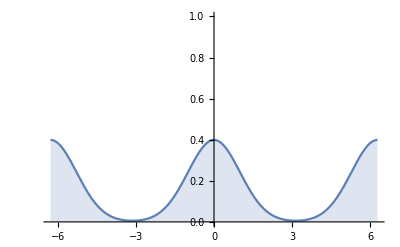

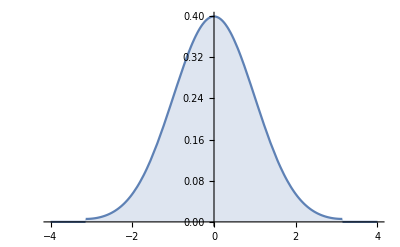

```mathematica
Plot[WrappedNormalPDF[x,1.0], {x,-2π,2π},Filling->Axis,PlotRange->{0.0,1.0}]
Plot[PDF[WNDist[1.0],x], {x,-4,4},Filling->Axis,PlotRange->Full]
(*Plot[WNDist[1.0], {x,-π,π},Filling->Axis,PlotRange->Full]*)
```

```mathematica
Manipulate[Plot[PDF[WNDist[σ],x],{x,-π,π},Filling->Axis,PlotRange->{0,4.0}],{{σ,0.2},0.01,1}]
```

```mathematica
σ = 0.1
sampleSize=10000;

anglesTable=RandomVariate[WNDist[σ],sampleSize];
(*normalsTable=Table[{Sin[anglesTable[[i]]],Cos[anglesTable[[i]]]},{i,1,Length[anglesTable]}];
Table[Norm[normalsTable[[i]]],{i,1,Length[normalsTable]}];
averageLength=Sum[normalsTable[[i]][[2]],{i,1,Length[normalsTable]}]/Length[normalsTable]
*)
```

0.1

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate

```mathematica
averageLength=Sum[Cos[anglesTable[[i]]],{i,1,Length[anglesTable]}]/Length[anglesTable]
```

0.995047

```mathematica
pipoSize = 100;
g[σ_]:=Sum[Cos[RandomVariate[WNDist[σ]]],{i,1,pipoSize}]/pipoSize
```

```mathematica
g[0.4]
```

0.935829

```mathematica
agnaTable=Table[{σ,g[σ]},{σ,0.01,4,0.1}]
```

{{0.01,0.999954},{0.11,0.99521},{0.21,0.977523},{0.31,0.95309},{0.41,0.933072},{0.51,0.879299},{0.61,0.803077},{0.71,0.73621},{0.81,0.658499},{0.91,0.564494},{1.01,0.616363},{1.11,0.443228},{1.21,0.493497},{1.31,0.457467},{1.41,0.40611},{1.51,0.307141},{1.61,0.277634},{1.71,0.377555},{1.81,0.179498},{1.91,0.0785861},{2.01,0.197142},{2.11,0.227309},{2.21,-0.0352354},{2.31,0.0757025},{2.41,-0.0437933},{2.51,0.125613},{2.61,-0.0691715},{2.71,0.0458541},{2.81,0.0367054},{2.91,0.0485791},{3.01,0.118479},{3.11,0.0513369},{3.21,-0.0975703},{3.31,0.030396},{3.41,-0.0026851},{3.51,-0.0921871},{3.61,0.0950734},{3.71,0.118039},{3.81,-0.103162},{3.91,-0.0580973}}

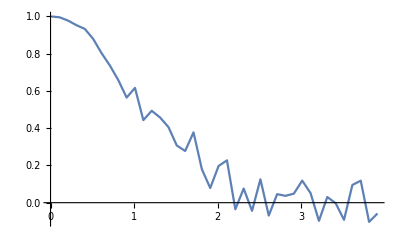

```mathematica
ListLinePlot[agnaTable]
```

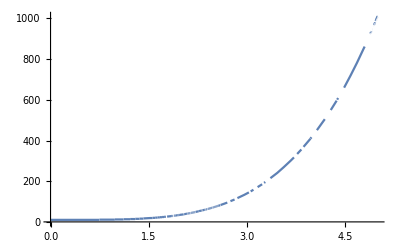

```mathematica
SigmaToCount[σ_]:=10+Round[(σ/5)^4*1000]
Plot[SigmaToCount[σ],{σ,0,5}]
```

```mathematica
h[σ_]:=Sum[Cos[RandomVariate[WNDist[σ]]],{i,1,SigmaToCount[σ]}]/SigmaToCount[σ]
```

```mathematica
testicule=Table[{σ,h[σ]},{σ,0.01,5,0.2}]
```

{{0.01,0.999969},{0.21,0.978597},{0.41,0.94048},{0.61,0.753123},{0.81,0.794911},{1.01,0.582739},{1.21,0.570707},{1.41,0.436168},{1.61,0.13237},{1.81,0.368843},{2.01,0.132858},{2.21,0.152298},{2.41,0.0360644},{2.61,0.25755},{2.81,0.124834},{3.01,0.0103645},{3.21,-0.0731705},{3.41,0.0421929},{3.61,0.101029},{3.81,0.0192396},{4.01,-0.00775454},{4.21,0.00210246},{4.41,0.0259837},{4.61,0.00782895},{4.81,-0.0457492}}

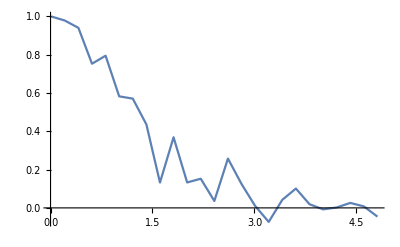

```mathematica
ListLinePlot[testicule]
```

```mathematica
SigmaToCount[σ_]:=10+Round[(σ/5)^2*1000]
glou=Table[Cos[0.5*RandomVariate[WNDist[σ]]],{i,1,10000}]

i[σ_]:=Sum[Cos[0.5*RandomVariate[WNDist[σ]]],{i,1,SigmaToCount[σ]}]/SigmaToCount[σ]
```

$Aborted

```mathematica
encumoule=Table[{σ,i[σ]},{σ,0.01,5,0.1}]
```

{{0.01,0.999993},{0.11,0.997866},{0.21,0.994627},{0.31,0.984701},{0.41,0.980142},{0.51,0.948638},{0.61,0.947211},{0.71,0.934823},{0.81,0.95162},{0.91,0.914266},{1.01,0.780548},{1.11,0.856867},{1.21,0.877413},{1.31,0.773217},{1.41,0.801112},{1.51,0.790008},{1.61,0.7694},{1.71,0.766957},{1.81,0.560611},{1.91,0.737168},{2.01,0.625901},{2.11,0.595995},{2.21,0.687291},{2.31,0.637423},{2.41,0.722811},{2.51,0.737531},{2.61,0.77437},{2.71,0.799438},{2.81,0.648397},{2.91,0.62802},{3.01,0.603415},{3.11,0.641062},{3.21,0.679068},{3.31,0.665077},{3.41,0.557043},{3.51,0.67687},{3.61,0.612562},{3.71,0.526476},{3.81,0.624176},{3.91,0.704534},{4.01,0.64596},{4.11,0.614341},{4.21,0.673406},{4.31,0.614385},{4.41,0.655038},{4.51,0.651257},{4.61,0.541912},{4.71,0.647499},{4.81,0.633518},{4.91,0.667858}}

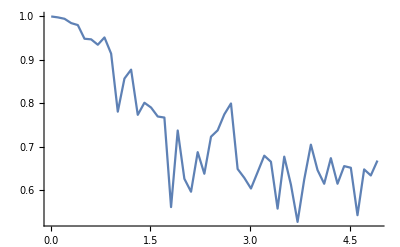

```mathematica
ListLinePlot[encumoule]
```